101

Analysis done!

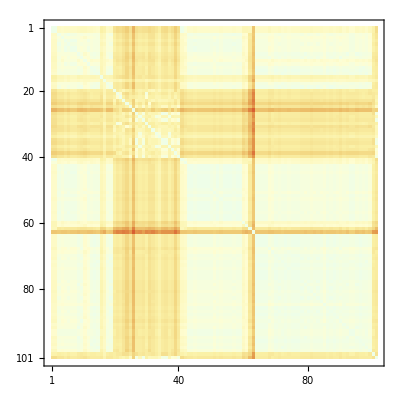

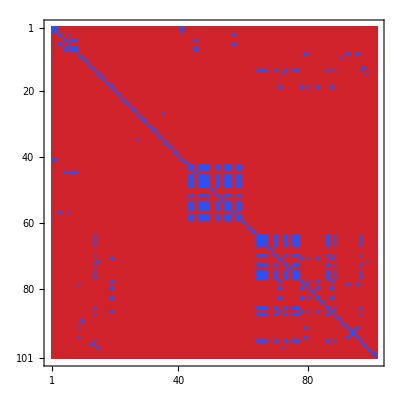

26

Clupea harengus RRM

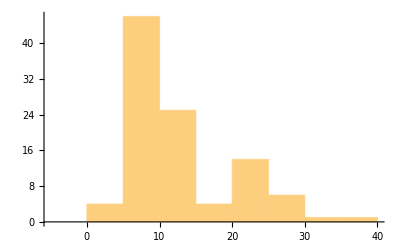

-Graphics-

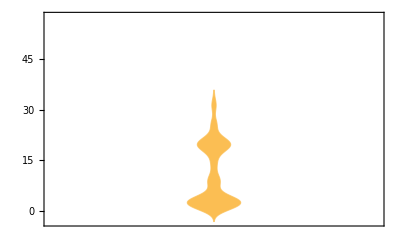

Average Edit Distance: 11.1083 +/- 9.47251

Median Edit Distance: 8. +/- 7.

RRM_DistributionGraph.pdf

```mathematica
(* Provide input file path *)

Datei="Unique species RRMs.fasta";

Sequenzen=Import[Datei,"Sequence"];
Header=Import[Datei,"Header"];
Length[Header]

Distances={};
Do[{a1=Sequenzen[[a]],
temp={};
Do[{b1=Sequenzen[[b]],
dist=EditDistance[a1,b1],
temp=AppendTo[temp,dist]
},{b,1,Length[Sequenzen]}],
Distances=AppendTo[Distances,temp]
},{a,1,Length[Sequenzen]}]
Print[Style["Analysis done!",Bold,Blue]]



(* Plot the data *)

MatrixPlot[Distances,ColorFunction->"LightTemperatureMap"]
MatrixPlot[Distances,ColorFunction->"TemperatureMap",ColorFunctionScaling->False]

pos=Flatten[Position[Distances[[1]],Max[Distances[[1]]]]][[1]]
Header[[pos]]

Histogram[Distances[[1]]]
Histogram[Distances[[1]]]
ExpGraphik=DistributionChart[{0,Flatten[Distances],0},
PlotRange->{{1,6},{Automatic,40}}]

UbDistances=Flatten[Distances];

Print[Style["Average Edit Distance: ",Bold,Blue],
N[Mean[UbDistances]]," +/- ",
N[StandardDeviation[UbDistances]]]

Print[Style["Median Edit Distance: ",Bold,Blue],
N[Median[UbDistances]]," +/- ",
N[MedianDeviation[UbDistances]]]


SetDirectory[DirectoryName[Datei]];
Export["RRM_DistributionGraph.pdf",ExpGraphik]
```

Ailuropoda melanoleuca RRM | 1
Alligator sinensis RRM | 1
Amazona aestiva RRM | 1
Anas platyrhynchos RRM | 1
Apaloderma vittatum RRM | 1
Aptenodytes forsteri RRM | 1
Apteryx australis mantelli RRM | 1
Balaenoptera acutorostrata scammoni RRM | 1
Bos taurus RRM | 1
Callithrix jacchus RRM | 1
Calypte anna RRM | 1
Caprimulgus carolinensis RRM | 1
Cariama cristata RRM | 1
Cercocebus atys RRM | 1
Chaetura pelagica RRM | 1
Charadrius vociferus RRM | 1
Chlamydotis macqueenii RRM | 1
Chrysemys picta bellii RRM | 1
Chrysochloris asiatica RRM | 1
Colius striatus RRM | 1
Columba livia RRM | 1
Condylura cristata RRM | 1
Corvus cornix cornix RRM | 1
Cuculus canorus RRM | 1
Dasypus novemcinctus RRM | 1
Equus caballus RRM | 1
Erinaceus europaeus RRM | 1
Eurypyga helias RRM | 1
Falco peregrinus RRM | 1
Felis catus RRM | 1
Ficedula albicollis RRM | 1
Gallus gallus RRM | 1
Heterocephalus glaber RRM | 1
Homo sapiens RRM | 1
Jaculus jaculus RRM | 1
Lepidothrix coronata RRM | 1
Loxodonta africana RRM | 1
Meleagris gallopavo RRM | 1
Melopsittacus undulatus RRM | 1
Miniopterus natalensis RRM | 1
Mus musculus RRM | 1
Myotis lucifugus RRM | 1
Nestor notabilis RRM | 1
Nomascus leucogenys RRM | 1
Ophiophagus hannah RRM | 1
Opisthocomus hoazin RRM | 1
Ornithorhynchus anatinus RRM | 1
Orycteropus afer afer RRM | 1
Ovis aries musimon RRM | 1
Ovis aries RRM | 1
Pantholops hodgsonii RRM | 1
Pelecanus crispus RRM | 1
Pelodiscus sinensis RRM | 1
Phaethon lepturus RRM | 1
Phoenicopterus ruber ruber RRM | 1
Picoides pubescens RRM | 1
Pongo abelii RRM | 1
Pseudopodoces humilis RRM | 1
Pterocles gutturalis RRM | 1
Pteropus alecto RRM | 1
Pygoscelis adeliae RRM | 1
Python bivittatus RRM | 1
Sarcophilus harrisii RRM | 1
Sorex araneus RRM | 1
Struthio camelus australis RRM | 1
Sturnus vulgaris RRM | 1
Sus scrofa RRM | 1
Taeniopygia guttata RRM | 1
Tauraco erythrolophus RRM | 1
Thamnophis sirtalis RRM | 1
Tinamus guttatus RRM | 1
Ursus maritimus RRM | 1
Zonotrichia albicollis RRM | 1
Astyanax mexicanus RRM | 2
Austrofundulus limnaeus RRM | 2
Callorhinchus milii RRM | 2
Clupea harengus RRM | 2
Cyprinodon variegatus RRM | 2
Elephantulus edwardii RRM | 2
Esox lucius RRM | 2
Ictalurus punctatus RRM | 2
Kryptolebias marmoratus RRM | 2
Larimichthys crocea RRM | 2
Lepisosteus oculatus RRM | 2
Microcebus murinus RRM | 2
Nothobranchius furzeri RRM | 2
Notothenia coriiceps RRM | 2
Octodon degus RRM | 2
Oreochromis niloticus RRM | 2
Oryzias latipes RRM | 2
Poecilia formosa RRM | 2
Poecilia mexicana RRM | 2
Pundamilia nyererei RRM | 2
Pygocentrus nattereri RRM | 2
Salmo salar RRM | 2
Sinocyclocheilus anshuiensis RRM | 2
Sinocyclocheilus grahami RRM | 2
Sinocyclocheilus rhinocerous RRM | 2
Stegastes partitus RRM | 2
Xenopus laevis RRM | 2
Xiphophorus maculatus RRM | 2

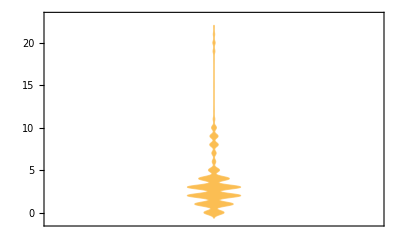

Average Edit Distance: 3.56577 +/- 3.61317

Median Edit Distance: 3. +/- 1.

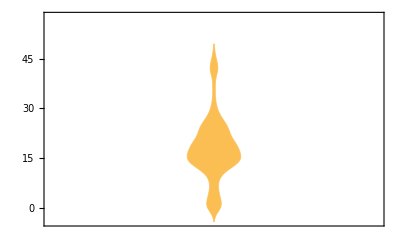

Average Edit Distance: 18.0153 +/- 9.68652

Median Edit Distance: 17. +/- 5.

```mathematica
(* Cluster analysis*)

TableForm[SortBy[Transpose[{Header,ClusteringComponents[Distances,2][[1]]}],Last]]
ClusterSeq=SortBy[Transpose[{Sequenzen,ClusteringComponents[Distances,2][[1]]}],Last];

(* Analyze sequences in cluster 1*)
TempCluster1=Select[ClusterSeq,#[[2]]==1&];
Cluster1=Transpose[TempCluster1][[1]];
Cl1dist={};
Do[{a1=Cluster1[[a]],
temp={};
Do[{b1=Cluster1[[b]],
dist=EditDistance[a1,b1],
temp=AppendTo[temp,dist]
},{b,1,Length[Cluster1]}],
Cl1dist=AppendTo[Cl1dist,temp]
},{a,1,Length[Cluster1]}]
DistributionChart[{0,Flatten[Cl1dist],0},
PlotRange->{{1,6},{Automatic,40}}]
Print[Style["Average Edit Distance: ",Bold,Blue],
N[Mean[Flatten[Cl1dist]]]," +/- ",
N[StandardDeviation[Flatten[Cl1dist]]]]
Print[Style["Median Edit Distance: ",Bold,Blue],
N[Median[Flatten[Cl1dist]]]," +/- ",
N[MedianDeviation[Flatten[Cl1dist]]]]

(* Analyze sequences in cluster 2*)
TempCluster2=Select[ClusterSeq,#[[2]]==2&];
Cluster2=Transpose[TempCluster2][[1]];
Cl2dist={};
Do[{a1=Cluster2[[a]],
temp={};
Do[{b1=Cluster2[[b]],
dist=EditDistance[a1,b1],
temp=AppendTo[temp,dist]
},{b,1,Length[Cluster2]}],
Cl2dist=AppendTo[Cl2dist,temp]
},{a,1,Length[Cluster2]}]
DistributionChart[{0,Flatten[Cl2dist],0},
PlotRange->{{1,6},{Automatic,40}}]
Print[Style["Average Edit Distance: ",Bold,Blue],
N[Mean[Flatten[Cl2dist]]]," +/- ",
N[StandardDeviation[Flatten[Cl2dist]]]]
Print[Style["Median Edit Distance: ",Bold,Blue],
N[Median[Flatten[Cl2dist]]]," +/- ",
N[MedianDeviation[Flatten[Cl2dist]]]]
```